```mathematica
Solve[Sin[(2 π)/T t]+k==0,t]
```

{{t→ConditionalExpression[(T (-ArcSin[k]+2 π C[1]))/(2 π),C[1]∈Integers]},{t→ConditionalExpression[(T (π+ArcSin[k]+2 π C[1]))/(2 π),C[1]∈Integers]}}

```mathematica
c=1;
(1(-ArcSin[1/2]+2 π 0))/(2 π)
(1 (π+ArcSin[1/2]+2 π 0))/(2 π)
```

-1/12

7/12

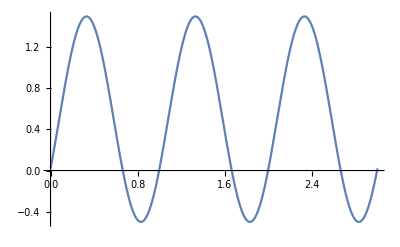

```mathematica
Plot[Sin[((2 π)/1)t-(1/2)]+1/2,{t,0,3}]
```

```mathematica
(1(-ArcSin[0.5]+2 π ))/(2 π)
```

0.916667

```mathematica
(1 (π+ArcSin[0.5]))/(2 π)
```

0.583333

```mathematica
1/1.5
```

0.666667

```mathematica
(T(π+ArcSin[k]+2 π c))/(2 π)-(T(-ArcSin[k]+2 π c))/(2 π)
```

-(T (2 π-ArcSin[k]))/(2 π)+(T (3 π+ArcSin[k]))/(2 π)

```mathematica
Simplify[-(T (2 π-ArcSin[k]))/(2 π)+(T (3 π+ArcSin[k]))/(2 π)]
```

T/2+(T ArcSin[k])/π

```mathematica
Solve[T/2+(T ArcSin[k])/π==2/3 T,k]
```

{{k→1/2}}

```mathematica
Sin[((2 π)/1)1-(1/2)]+1/2//N
```

0.0205745

```mathematica
Plot[Sin[(2π)/1(t-θ)]+1/2,{t,-2,2}]
```

-Graphics-

```mathematica
Solve[Sin[(2π)/T(θ)]+1/2==1,θ]
```

{{θ→ConditionalExpression[(T (π/6+2 π C[1]))/(2 π),C[1]∈Integers]},{θ→ConditionalExpression[(T ((5 π)/6+2 π C[1]))/(2 π),C[1]∈Integers]}}

```mathematica
Manipulate[Plot[-Sin[(2π)/T(t-(T (π/6))/(2 π))]-1/2,{t,-5,5}],{T,3,10}]
```

```mathematica
f[t_]:=Sin[(2π)/T(t-T/12)]+1/2
```

```mathematica
f[(2T)/3]
```

0

```mathematica
1/2+Sin[(11 π T)/18]
```

1/2+Sin[(11 π T)/18]

```mathematica
TrigReduce[1/2+Sin[(11 π T)/18]]
```

1/2 (1+2 Sin[(11 π T)/18])